(g m^2)/b^2-(g m^2 Log[(m v0 Cos[θ])/(-b x+m v0 Cos[θ])])/b^2-(g m (-b x+m v0 Cos[θ]) Sec[θ])/(b^2 v0)+(m v0 Sin[θ])/b-((-b x+m v0 Cos[θ]) Tan[θ])/b

341.714-108.481 (3.15-0.033 x)-176.382 Log[3.15/(3.15-0.033 x)]

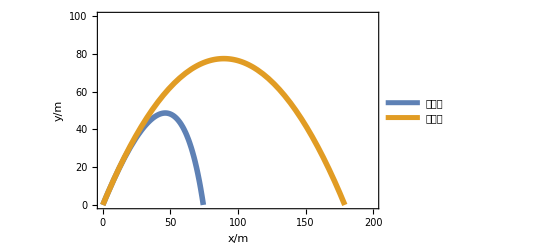

```mathematica
Clear["Global`*"]
sol = DSolve[{x''[t] == -(b/m)*x'[t], y''[t] == -(b/m)*y'[t] - g, x[0] == 0, y[0] == 0, x'[0] == v0*Cos[θ], y'[0] == v0*Sin[θ]}, {x[t], y[t]}, t]//ExpandAll;
(*运动方程求解*)
x[t_]=(x[t]/.Flatten[sol][[1]]);
y[t_]=(y[t]/.Flatten[sol][[2]]);
t[t_]=InverseFunction[x][t]//Simplify;
(*反函数，利用x表示t*)
yx[x_]=y[t[x]]
(*t(x)带入y(t)，获得表达式y(x)*)
yyx[x_]=yx[x]//.{b->0.033,m->0.14,v0->45,θ->π/3,g->9.8}
(*赋值*)
yy0[x_]=Tan[θ]*x-(1/2)*(g/(v0^2*Cos[θ]^2))*x^2//.{g->9.8,v0->45,θ->π/3};
(*无阻力轨迹方程*)
Plot[{yyx[x],yy0[x]},{x,0,200},PlotStyle->Thickness[0.01],PlotRange->{{0,200},{0,100}},Frame->True,FrameLabel->{Style["x/m",18],Style["y/m",18]},FrameStyle->Thickness[0.003],PlotLegends->{Style["有阻力",18],Style["无阻力",18]}]
(*绘图*)
```